## Моделирование методом Монте - Карло

### Вероятность дня рождения у двух человек методом Монте - Карло

Пусть у нас есть группа из 48 человек ровестников одного года рождения (например у всех 2001 год рождения). Какова вероятность того, что в группе попадутся те, у кого дни рождения совпадают?

```mathematica
groupMonteKarlo[childrends_, experiments_]:=Module[{a=childrends,b=experiments},
counterPeoplesInGroup=a;
counterExperiments = b;
counterSuccessFullExperiments=0;
For[i=1,i<=counterExperiments,i++,
lst=Table[Random[Integer,{1,365}],{i,1,counterPeoplesInGroup}];If[Length[lst]!=Length[DeleteDuplicates[lst]],counterSuccessFullExperiments+=1]
];
Print["Количество экспериментов: ", counterExperiments];
Print["Количество экспериментов, в которых даты рождения совпали ", counterSuccessFullExperiments];
Print["Вероятность, что в группе из ",counterPeoplesInGroup, " человек будут те, у которых день рождения совпадает: p = ", 
counterSuccessFullExperiments, " / ", counterExperiments, " * 100% = ", N[counterSuccessFullExperiments/counterExperiments * 100], "%"];
N[counterSuccessFullExperiments/counterExperiments]
]
```

```mathematica
groupMonteKarlo[24,100000]
```

Количество экспериментов: 100000

Количество экспериментов, в которых даты рождения совпали 53644

Вероятность, что в группе из 24 человек будут те, у которых день рождения совпадает: p = 53644 / 100000 * 100% = 53.644%

0.53644

```mathematica
groupMonteKarlo[48,100000]
```

Количество экспериментов: 100000

Количество экспериментов, в которых даты рождения совпали 96029

Вероятность, что в группе из 48 человек будут те, у которых день рождения совпадает: p = 96029 / 100000 * 100% = 96.029%

0.96029

### Площадь известной фигуры методом Монте - Карло

Вычислить площадь фигуры x^2+y^2=R^2, у которой есть ограничения x>=0 и y>=0, где R дано.

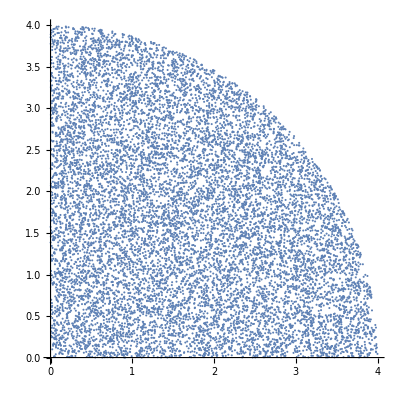

Методом Монте-Карло получили площадь равную 12.445 (в оригинале она равна 12.5664)

```mathematica
xmin=-5;
xmax=5;
ymin=-5;
ymax=5;
R=4;
counter=0;
counterExperiments=100000;
lst={};
For[i=1,i<=counterExperiments,i++,
x=Random[Real,{xmin,xmax}];
y=Random[Real,{ymin,ymax}];
If[x^2+y^2<=R^2 && y>=0&&x>=0,
counter+=1;
lst=Join[{{x,y}},lst]
]
]
squareMonteKarlo=N[(Abs[xmin]+Abs[xmax])*(Abs[ymin]+Abs[ymax])*counter/counterExperiments];
squareOriginal=N[Pi*R^2/2/2];
ListPlot[lst,AspectRatio->Automatic]
Print["Методом Монте-Карло получили площадь равную ", squareMonteKarlo, " (в оригинале она равна ", squareOriginal, ")"]
```

### Площадь произвольный фигуры методом Монте - Карло

Найти площадь фигуры на промежутке от -7 до 7 заданой формулами sin(x) и y>0

Методом Монте-Карло получили площадь равную 3.95049

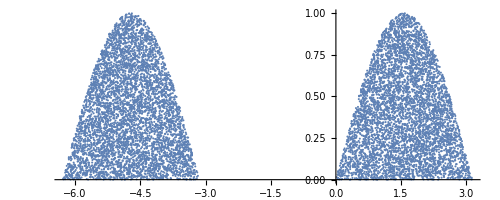

```mathematica
xmin=-2Pi;
xmax=2*Pi;
ymin=-1.5;
ymax=1.5;
counter=0;
counterExperiments=100000;
lst={};
For[i=1,i<=counterExperiments,i++,
x=Random[Real,{xmin,xmax}];
y=Random[Real,{ymin,ymax}];
If[Sin[x]>=y && y>=0,
counter+=1;
lst=Join[{{x,y}},lst]]
]
squareMonteKarlo=N[(Abs[xmin]+Abs[xmax])*(Abs[ymin]+Abs[ymax])*counter/counterExperiments];
Print["Методом Монте-Карло получили площадь равную ", squareMonteKarlo];
ListPlot[lst,AspectRatio->Automatic]
```

## Descriptive Statistics - Описательная статистика

### Mean

Mean = 1/n∑_(i=1)^n xi

```mathematica
Mean[{1,2,3,4,5,6,100}]
Mean[{1,2,3,4,5,6,100}]//N
```

121/7

17.2857

### Median

```mathematica
Median[{1,2,3,4,5,6,100}]
```

4

### Commonest

Commonest - получить элементы с наибольшей частотой

```mathematica
Commonest[{1,2,3,4,5,6,7,1,1,1,1,5,5,5,4,4,4,4,4,1}]
```

{1,4}

### GeometricMean

GeometricMean - среднее геометрическое столбцов матрицы
(∏_(i=1)^n xi)^(1/n)

```mathematica
GeometricMean[{1,2,3,4}]
GeometricMean[{1,2,3,4}] //N
(1 2 3 4)^(1/4) //N
```

2^(3/4) 3^(1/4)

2.21336

2.21336

```mathematica
GeometricMean[{5,6,7,8}]
GeometricMean[{5,6,7,8}] //N
(5 6 7 8)^(1/4) //N
```

2 105^(1/4)

6.40217

6.40217

```mathematica
GeometricMean[{{1,5},{2,6},{3,7},{4,8}}]
GeometricMean[{{1,5},{2,6},{3,7},{4,8}}] //N
```

{2^(3/4) 3^(1/4),2 105^(1/4)}

{2.21336,6.40217}

### HarmonicMean

n/(∑_(i=1)^n xi^2)

```mathematica
HarmonicMean[{1,2,3,4}]
HarmonicMean[{1,2,3,4}] //N
4/(1/1+1/2+1/3+1/4)
4/(1/1+1/2+1/3+1/4)//N
```

48/25

1.92

48/25

1.92

### RootMeanSquare

√(1/n∑_(i=1)^n xi^2)

```mathematica
RootMeanSquare[{1,2,3,4}]
RootMeanSquare[{1,2,3,4}]//N
√(1/4(1^2+2^2+3^2+4^2))
√(1/4(1^2+2^2+3^2+4^2))//N
```

√(15/2)

2.73861

√(15/2)

2.73861